# Harrow–Hassidim–Lloyd (HHL) Algorithm

Numerically solve a system of linear equations using a quantum algorithm

## Example Content

The HHL algorithm is a quantum algorithm designed to solve systems of linear equations. Given a matrix A and a vector b, it tries to solve A·x=b.

Install the QuantumFramework paclet:

```mathematica
PacletInstall["Wolfram/QuantumFramework"]
```

PacletObject[…]

Load the paclet:

```mathematica
Needs["Wolfram`QuantumFramework`"]
```

Consider a Hermitian operator of 2-qubits, a random vector b and 6 ancillary qubits:

```mathematica
prec=6;
A={{0.21,0.15,0.07,0.},{0.15,0.38,0.18,0.07},{0.07,0.18,0.19,0.04},{0.,0.07,0.04,0.22}};
b=Round[RandomReal[1,2^2],0.01];
```

Generate an HHL circuit that takes  A,  b and number of ancillary qubits  prec:

```mathematica
hhl=Block[{d=Log2@Length[b],qpe},
QuantumCircuitOperator[{
QuantumCircuitOperator[{QuantumState[Normalize[b]]->1+prec+Range[d]},"State preparation"],
qpe=QuantumCircuitOperator["PhaseEstimation"[QuantumOperator[MatrixExp[2Pi I A]],prec],1+Range[prec+d]][[d+1;;-prec-1]],
QuantumCircuitOperator["GrayOracle"[If[#==0,0,1./#]&,prec,1],"Eigenvalue Inversion"],
qpe["Dagger"],
QuantumOperator[{QuantumState["Register"[prec+1,2^prec]]["Dagger"]->Range[prec+1]},"Label"->"Post-selection"]
}]];
```

Show the HHL circuit diagram:

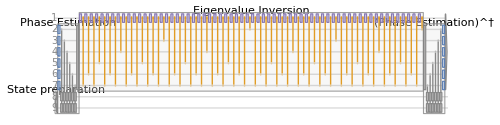

```mathematica
hhl["Diagram","ShowGateLabels"->False, ]
```

Given the result of the above circuit, find the corresponding probabilities, and then their square roots to get the solution with the HHL solver:

```mathematica
Sqrt@hhl[]["ProbabilitiesList"]
```

{0.642053,0.72234,0.176279,0.186864}

Although the probabilities can be measured experimentally, they do not all have the correct signs.

Find the corresponding amplitudes, and then normalize them to get the solution with the HHL solver:

This input keeps failing for me. Can you check that it's correct? (I have v1.3.6 of the paclet)

I revised hhl code. Plz check and let me know :-)

```mathematica
Normalize@Values@hhl[]["Amplitudes"]//Chop
```

{0.642053,0.72234,0.176279,-0.186864}

Find the corresponding solution using the classical approach:

```mathematica
Normalize@LinearSolve[A,b]
```

{0.641359,0.722972,0.172766,-0.190057}

Although with amplitudes, one gets the right answers (with correct signs), but the amplitudes are not accessible experimentally.

## Supporting Data and Definitions

(Your data can be Dataset[…], EntityStore[…], Image[…], Audio[…] or any other expression)

(xxxx can be your data, or File[…], CloudObject[…] or LocalObject[…] that contains it.)

## Thumbnail Image

```mathematica
hhl["Diagram","ShowGateLabels"->False, AspectRatio->1/4,ImageSize->{Automatic,250}]
```

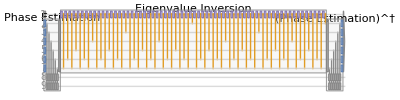
```mathematica
ImageCrop[-Graphics-,{500,500},Right]
```

## Source & Additional Information

### Contributed By

Wolfram Research, Quantum Computation Framework Team

### Keywords

Harrow–Hassidim–Lloyd (HHL) algorithm

Quantum linear solver

### Categories

Algebra
 Calculus
 Complex Systems
 Control Systems
 Engineering
 Food & Nutrition
 Graphs & Networks
 Machine Learning
 Optimization
 Puzzles and Recreation
 Social Sciences
 Time-Related Computation
  |  Astronomy
 Cellular Automata
 Computer Science
 Creative Arts
 Finance & Economics
 Geography
 Image Processing
 Mathematics
 Physics
 Quantum Computation
 System Modeling
 Video Processing
 |  Audio Processing
 Chemistry
 Computer Vision
 Data Science
 Finite Element Method
 Geometry
 Life Sciences
 Notebooks & User Interfaces
 Presentation & Publication
 Signal Processing
 Text & Language Processing
 Visualization & Graphics

### Related Documentation Pages

Symbol name or documentation URI

### Related Resource Objects

Wolfram/QuantumFramework/

### Original Source References and Attributions

Source, reference or citation

### Links

### Compatibility

#### Wolfram Language Version

13.2+

#### Operating System

Windows |  Mac |  Linux

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

## Author Notes

Additional information about limitations, issues, etc.